# Financial Econometrics I

Modeling Volatility II

## (Lecture 5)

Summer Semester 2025/2026 by Lukas Vacha

join online lecture in MS Teams

* If viewed in .pdf format - for full functionality use Mathematica 7 notebook (.nb) version of this .pdf

## Conditional Heteroscedastic Models - II

Conditional heteroscedastic models are used for modeling σ_t^2 as an volatility estimate by "allowing" heteroscedasticity (time-variation) and capturing that dependence.

Discussion of the reading
IGARCH
Forecasting with GARCH
EWMA
GARCH-t
TAR-GARCH
EGARCH
Introduction to Long memory
Long memory in volatility

## IGARCH - Integrated GARCH

### Motivating example: two samples with different unconditional variance (SPX index):

We can clearly observe different levels of GARCH model persistence (sum of α and β)

Sample 1: 1/02/1950 12/31/1953:
	σ_t^2=0.000011+0.64 σ_(t-1)^2+0.14 a_(t-1)^2,  	t-dof = 5.079.
Sample 2: 1/02/2007 12/31/2010:
	σ_t^2=0.0000017+0.9007 σ_(t-1)^2+0.09989 a_(t-1)^2, t-dof = 5.651.

-Graphics--Graphics-

#### Where do we need IGARCH?

IGARCH models are unit-root (integrated) GARCH models where α_1+β_1=1, their key feature is, that past squared shocks are persistent. The unconditional variance of a_t is not defined under the IGARCH(1,1) model specification. 

The IGARCH effect might be caused by level shifts in volatility, i.e., can be spurious, (for example long samples. Similar to simple AR processes.) see Mikosch and Stărică (2004).

IGARCH(1,1) is defined as:

a_t=σ_t ϵ_t,
σ_t^2=α_0+β_1 σ_(t-1)^2+(1-β_1)a_(t-1)^2, 
where 0<β_1<1

For α_0=0, the IGARCH(1,1) → infinite EWMA.

### Example IGARCH(1,1) artificial processes

## Forecasting with GARCH

GARCH(1,1) is most common for financial applications. The volatility equation combines connection with past returns as well as autoregressive dependence.

a_t=σ_t ϵ_t,
σ_t^2=α_0+α_i a_(t-1)^2+β_1 σ_(t-1)^2, 

Forecasts of the GARCH can be obtained recursively
at origin h, the 1-step ahead forecast of σ_(h+1)^2 is:

σ_(h+1)^2=α_0+α_1 a_h^2+β_1 σ_h^2

For multi-forecast, we use a_t^2=σ_t^2 ϵ_t^2 and since E(ϵ_(h+1)^2|F_h)=1, we have,

σ_(h+1)^2   =α_0+(α_1+β_1)σ_h^2
σ_(h+2)^2   =α_0+(α_1+β_1)σ_(h+1)^2
σ_(h+l+1)^2=α_0+(α_1+β_1)σ_(h+l)^2,   l>1

σ_(h+l)^2→α_0/(1-α_1-β_1),  as  l→∞.  
Hence, the forecast converges to the unconditional variance.

## Forecasting with the Exponential Moving Average (EWMA)

Alternatively, exponential moving average (EWMA) estimator of volatility can be used. It uses all data points, and recent observations carry larger weights. (weights are exponentially decreasing). It also has the effect of diminishing the problematic “Ghost Features”.

An m-period EWMA with smooth constant λ is defined as:

σ_t^2=(∑_(τ=1)^m λ^(τ-1)r_(t-1-τ)^2)/(1+λ^1+...+λ^(m-1))  where 0<λ<1
σ_(t+1|t)^2=(1-λ)∑_(τ=0)^∞ λ^τ r_(t-τ)^2   as m→∞,
σ_(t+1|t)^2=(1-λ)r_t^2+λ(1-λ)(∑_(τ=1)^∞ λ^(τ-1)r_(t-τ)^2)  
using the approximation  ∑_(τ=1)^∞ λ^(τ-1)≃1/(1-λ)  we get: 

σ_(t+1|t)^2=(1-λ)r_t^2+λσ_(t|t-1)^2,

where the initial value could be unconditional variance in a historical sample. 
In most financial applications, λ=0.94 is used.

The EWMA model is equivalent to the IGARCH model, that is why the next day forecasts look very similar to forecasts based on GARCH type models.

The EWMA ignores the long-run variance (unconditional), while the forecasts based on GARCH family models converge in the long-run to the unconditional variance of the sample.
.00

σ_t^2=(1-λ)r_(t-1)^2+λσ_(t-1)^2,
where initial value could be unconditional variance in a historical sample. In most financial applications, λ=0.94 is used.

### Example 1 month, 1 year volatility of Apple.

### Example: Real financial market data -DAX index

Forecasts of variance for the DAX index. Two samples with different unconditional variance.

```mathematica
-Graphics--Graphics-
```

## GARCH with t innovations

Are the GARCH residuals normally distributed ? Usually the financial assets prices are fat-tailed, i.e. the distribution has more weight in the tails then a normal distribution. In general, there is a higher probability of large gain (or loss) then indicated by the normal distribution. 

Instead of the Gaussian innovations we can use t-distributed innovations.

### Example: with Q-Q plot

Apple (AAPL) daily closing prices GARCH(1,1), Q-Q plots of residuals against the quantiles of t-distribution (tdof=6.78) and the normal distribution:
-Graphics--Graphics-

## Threshold Autoregressive (TAR)-GARCH Model

Threshold Autoregressive (TAR) model can be used to refine the model by allowing for asymmetric response in the (volatility) equation to the sign of shock. We can observe asymmetry in declining and rising patterns of examined time series. Model uses simple threshold to improve linear approximation. We demonstrate the idea on a simple two regime AR(1) model and then we proceed to threshold model in the variance equation.

### Examples of Two Regime AR (1) model

Two-Regime AR(1) model is represented by:

x_t=Piecewise[{{α_1+β_1 x_(t-1)+ϵ_t, x_(t-1)<k}, {α_2+β_2 x_(t-1)+ϵ_t, x_(t-1)≥k}}]

Parameters are initially set to:  α_1=α_2=0, β_1=-1.5 and β_2=0.5 to obtain following Two Regime AR(1) process: 

x_t=Piecewise[{{-1.5 x_(t-1)+ϵ_t, x_(t-1)<0}, {0.5 x_(t-1)+ϵ_t, x_(t-1)≥0}}]

Note, that the process is stationary despite the coefficient -1.5 in the first regime. Series contains large upward jumps when it becomes negative (due to -1.5 coefficient), and there are more positive then negative ones. Model also contains no constant term, but E(x_t) is not zero.

```mathematica
Manipulate[
SeedRandom[seed];
Clear[x];random=RandomReal[NormalDistribution[0,1],500];x[1]=0;
tardat=With[{f={i,2,Length[random]}},Table[
If[x[i-1]<tresh,x[i]=alfa1+beta1 x[i-1] + random[[i]],x[i]=alfa2+beta2 x[i-1] + random[[i]]],f]];
ListPlot[tardat,
Joined->True,Frame->True,PlotStyle->{Thickness[Medium], Red},PlotRange->All],
Style["Two Regime AR(1) model",12,Bold],
{{tresh,0,"treshold - k"},-3,3,Appearance->"Labeled"},Delimiter,
{{alfa1,0,"α_1"},-3,3,Appearance->"Labeled"},
{{beta1,-1.5,"β_1"},-3,3,Appearance->"Labeled"},Delimiter,
{{alfa2,0,"α_2"},-3,3,Appearance->"Labeled"},
{{beta2,0.5,"β_2"},-3,3,Appearance->"Labeled"},
{{seed,77777,"New Random Case"},10000,999999,1},
Button["Export Simulated Series",Export["TAR1.txt",tardat],ImageSize->200],ControlPlacement->Top]
```

### Example

Set parameters of previous example to:  α_1=α_2=0, β_1=0.2 and β_2=0.9 to obtain following Two Regime AR(1) process 

x_t=Piecewise[{{0.2 x_(t-1)+ϵ_t, x_(t-1)<k}, {0.9 x_(t-1)+ϵ_t, x_(t-1)≥k}}]
and see the mixture of short-memory and long-memory processes

### Example of application: AR(1)-TAR-GARCH(1,1)

TAR models can be used for capturing asymmetric response in volatility. If we find the series to follow AR(1)-GARCH(1,1) process, we can introduce TAR to model asymmetric response in volatility to shocks. Model is formalized:

r_t=ϕ_0+ϕ_1 r_(t-1)+a_t,
a_t=σ_t ϵ_t
σ_t^2=Piecewise[{{α_0+α_1 a_(t-1)^2+β_1 σ_(t-1)^2, a_(t-1)≤0}, {α_2+α_3 a_(t-1)^2+β_2 σ_(t-1)^2, a_(t-1)>0}}]

```mathematica
Manipulate[
SeedRandom[seed];
random=RandomReal[NormalDistribution[0,1],500];
s=Table[0,{500}];r=Table[0,{500}];a=Table[0,{500}];
r[[1]]=random[[1]];s[[1]]=Variance[random];
Do[If[a[[i-1]]>tresh,s[[i]]=alfa2+alfa3 (r[[i-1]])^2 +beta2 s[[i-1]];,s[[i]]=alfa0+alfa1 (r[[i-1]])^2 +beta1 s[[i-1]];];
a[[i]]=Sqrt[s[[i]]] random[[i]];
r[[i]]=arconst+arp1 r[[i-1]]+a[[i]];
,{i,2,Length[random]}];
If[(alfa1+beta1)<1===True,If[(alfa3+beta2)<1===True,
ListPlot[If[type==="Simulated series",r,s],Joined->True,Frame->True,PlotStyle->{Thickness[Medium], Red},PlotRange->All],
Style["Please input (α_i+β_i)<1",Bold,12]],Style["Please input (α_i+β_i)<1",Bold,12]],
Style["AR(1)-TAR-GARCH(1,1)",12,Bold],
{{type,"Simulated series",""},{"Simulated series","Simulated Volatility"}},Delimiter,
{{tresh,0,"treshold - k"},-10,10,Appearance->"Labeled"},Delimiter,
{{arconst,0.6,"ϕ_0"},-3,3,Appearance->"Labeled"},
{{arp1,0.5,"ϕ_1"},-1,1,Appearance->"Labeled"},Delimiter,
{{alfa0,0.5,"α_0"},0.01,1,Appearance->"Labeled"},
{{alfa1,0.3,"α_1"},0,1,Appearance->"Labeled"},
{{beta1,0.2,"β_1"},0,1,Appearance->"Labeled"},Delimiter,
{{alfa2,0.5,"α_2"},0.01,1,Appearance->"Labeled"},
{{alfa3,0.3,"α_3"},0,1,Appearance->"Labeled"},
{{beta2,0.5,"β_2"},0,1,Appearance->"Labeled"},
{{seed,77777,"New Random Case"},10000,999999,1},
Button["Export Simulated Series",Export["Ar1_Tar_GARCH_11.txt",r],ImageSize->200],ControlPlacement->Top]
```

### GJR-GARCH

GJR-GARCH is a simple version of threshold GARCH model. The volatility equation has a form:
 
	σ_t^2=α_0+β_1 σ_(t-1)^2+α_1 a_(t-1)^2+γ I(a_(t-1)⩽0)a_(t-1)^2

where I is the indicator function.

### Empirical example

Apple (AAPL) daily closing prices sample: 9/1/2009 11/18/2011 (561 obs.)	

Estimated volatility eq. (normal innovations): σ_t^2=0.00005+0.665 σ_(t-1)^2+0.244 a_(t-1)^2 I(a_(t-1)⩽0)

Estimated volatility eq. (t innovations): σ_t^2=0.00004+0.71 σ_(t-1)^2+0.240 a_(t-1)^2 I(a_(t-1)⩽0)

where I(a_(t-1)<0)=1 if a_(t-1)<0.

## EGARCH Model

The EGARCH (Nelson, 1991) model be also used for capturing asymmetric response in volatility - the leverage effect. The EGARCH(m,s) can be defined as:
	
	a_t=σ_t ϵ_t
	
	ln(σ_t^2)=α_0+(1+α_1 L+...+α_m L^m)/(1-β_1 L...-β_s L^s)g(ϵ_(t-1))
	
	g(ϵ_t)=θ ϵ_t+γ[|ϵ_t|-E|ϵ_t|]
	

where α_0>0, θ,γ∈ℝ are real constants. For the standard Gaussian random variable ϵ_t , E|ϵ_t|=√(2/π).

Function g(.) captures the asymmetric relations between stock returns and volatility. It is both function of magnitude and sign of ϵ_t. Each component of g(ϵ_t) has mean zero. Thus, g(ϵ_t) is a zero mean i.i.d. random sequence.

When ϵ_t is positive (negative) g(ϵ_t) is linear in ϵ_t with slope θ+γ (θ-γ). Thus, g(ϵ_t) allows for asymmetrical response of conditional variance (σ_t^2) to positive or negative returns.


Example EGARCH(0,1)

	(1-β_1 L)ln(σ_t^2)=α_0+g(ϵ_(t-1))

## Long memory - motivation

Several disciplines came to realizations that naturally occurring phenomena (river flow, atmospheric patterns, telecommunications, economics, etc) exhibit correlations that do not decay at a sufficiently fast rate.

It is difficult to distinguish between I(1) and I(0). Thus, knife-edge distinction between I(0) and I(1) processes can be far too restrictive.

Volatility of asset prices can be successfully approximated by long memory models. 

Significant correlations in observations are separated by great periods of time.

Occurrence of jumps

Long memory time series require different approaches to modeling than the short memory time series.

Application to fin. markets: Ding, Zhuanxin, Clive WJ Granger, and Robert F. Engle. “A long memory property of stock market returns and a new model.” Journal of empirical finance 1.1 (1993): 83-106.

Example:
prediction of long memory process: Red line is prediction based on AR(3) and the yellow one is appropriate long memory process.

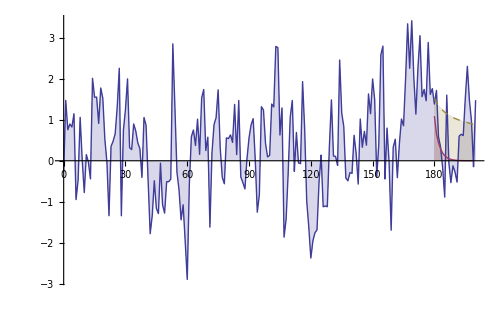

## Concept of Long memory

There are various definitions of long memory! We focus on a covariance structure of the process:
 
Definition: Let r_t be a stationary process for which the following holds. There exists a real number α∈(0,1) and a constant c_ρ>0 such that

	lim_(k⟶∞) (ρ(k))/[c_ρ k^-α]=1.

Then r_t is called a stationary process with long memory or long range dependence or strong dependence, or a stationary process with slowly decaying or long range correlations (Beran 1994). 

Further we use memory parameter d=(1-α)/2.

In case d=0, (α=1), then r_t is a random process with exponentially decaying ACF.

Example ACF of short and long memory process:

```mathematica
DiscretePlot[CorrelationFunction[FARIMAProcess[{.1},.49,{.3},1],h],{h,0,100},ExtentSize->1/1.5,PlotRange->All]
```

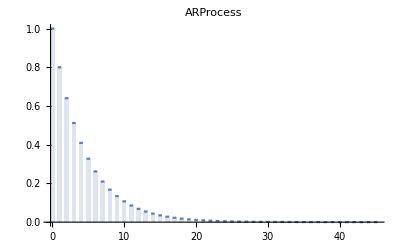
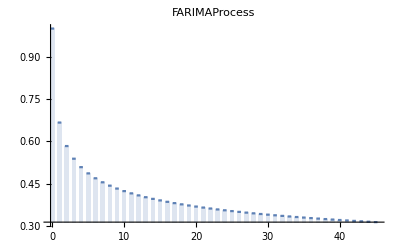

```mathematica
proc1=ARProcess[{.8},1];
proc4=FARIMAProcess[{},.4,{},1];
DiscretePlot[CorrelationFunction[#,h],{h,0,45},ExtentSize->1/2,PlotRange->All,PlotLabel->Head[#]]&/@{proc1,proc4}
```

Long memory:   0< d < .bd

Problems with long-memory detection: only the rate of convergence is defined, not the absolute size. 

Example: ACF plot with white-noise confidence bands

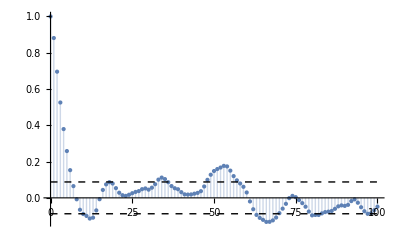

```mathematica
data=RandomFunction[FARIMAProcess[{.7},.19,{.3},1],{1,500}];
acf[data_,lmax_,clev_:0.95]:=Show[ListPlot[CorrelationFunction[data,{0,lmax}],Filling->Axis,PlotRange->{{0,lmax},All},PlotStyle->PointSize[Medium]],
Graphics[{Dashed,Line[{{0,#},{lmax,#}}]}]&/@(Quantile[NormalDistribution[],{(1-clev)/2,1-(1-clev)/2}]/(√(data["PathLengths"]⟦1⟧)))]
acf[data,100,.95]
```

## Fractional ARIMA

ARIMA model were introduced by Box and Jenkins in 1970.
 
Fractional ARIMA (ARFIMA, FARIMA) models are natural extension of the classic ARIMA.

ARMA (p, q):

	r_t=ϕ_0+∑_(i=1)^p ϕ_i r_(t-1)+ϵ_t-∑_(l=1)^q θ_i ϵ_(t-l)
or
	(1-ϕ_1 L -...-ϕ_p L^p)r_t=ϕ_0+(1+θ_1 L+...+θ_q L^q)ϵ_t
	
ARIMA (p, d, q):
Series are said to be ARIMA(𝓅,1,𝓆), when the process r_t-r_(t-1)=(1-L)r_t follows a stationary and invertible ARMA(𝓅,𝓆). Parameter 𝒹 is equal to 1, and means, that ARMA(𝓅,𝓆) series are differenced once (parameter d is an integer, d≥0).

	ϕ(L)(1−L)^d r_t=θ(L)ε_t

ARFIMA generalize ARIMA by allowing d to assume any real value.

Definition ARFIMA: Let r_t be a stationary process such that

	 (1−L)^d ϕ(L)r_t=θ(L)ε_t
	 
for some  -1/2<d<1/2. Then r_t is called a fractional ARIMA (p,d,q) process.

The parameter d determines the long-term behavior, parameters p and q allow for more flexible modelling of the short-range properties.

For (1−L)^d , where d is any real number we can write:

	(1−L)^d=∑_(k=0)^∞ (d
k)(−1)^k L^k   (d=H−1/2),

	(d
k)=(d!)/(k!(d−k)!)=(Γ(d+1))/(Γ(k+1)Γ(d−k+1)),
	
where  Γ(.) is Euler’s gamma function.

Thus, when we apply the fractional differencing operator (which is in fact a filter) we obtain:

	Z_t=(1−L)^d r_t=ϕ(L)^-1 θ(L)ε_t
 
 where Z_t is the ordinary ARMA(p,q) process.

### Example: Approximation of the ARFIMA process with the MA and AR process

```mathematica
MAProcess[FARIMAProcess[{0},.4,{.0},1],20]
```

MAProcess[{0.4,0.28,0.224,0.1904,0.167552,0.150797,0.137871,0.127531,0.119029,0.111887,0.105784,0.100495,0.0958568,0.0917487,0.0880787,0.0847758,0.0817837,0.0790576,0.076561,0.0742642},1]

```mathematica
ARProcess[FARIMAProcess[{0},.4,{.0},1],20]
```

ARProcess[{0.4,0.12,0.064,0.0416,0.029952,0.0229632,0.0183706,0.0151557,0.0127982,0.0110064,0.0096056,0.00848495,0.00757118,0.00681406,0.00617808,0.0056375,0.00517324,0.00477087,0.00441934,0.00410998},1]

### Example: Approximation of ARFIMA by an AR process

ARProcess[{1.7,-1.05,0.493,-0.2561,0.124722,-0.0633594,0.0316797,-0.0153806,0.00836388,-0.00341405,0.00250749,-0.000453279,0.00100987,0.000252185,0.000600741},1]

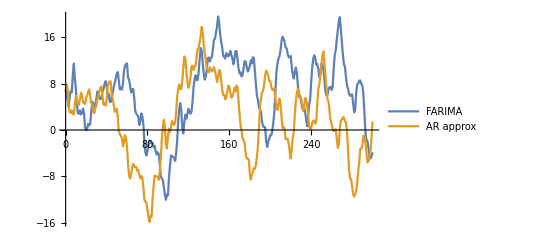

```mathematica
proc=FARIMAProcess[{.8},.4,{.5},1];
aproc=ARProcess[proc,15]
SeedRandom[13];sample=RandomFunction[proc,{300}];
SeedRandom[13];asample=RandomFunction[aproc,{300}];
ListLinePlot[{sample,asample},PlotLegends->{"FARIMA","AR approx"}]
```

### ACF for ARFIMA (0, d, 0)

ARFIMA (0, d, 0):   (1−L)^d r_t=ε_t

The autocorrelations of such a process decline at a hyperbolic rate to zero (0<d<1/2), a much slower rate of decay than the exponential decay of the ARMA process.The sum of the absolute values of the autocovariance function is infinite; this is the case of long memory or long range dependence (Hosking 1981).

Let us assume μ=E(r_t)=0, ϵ_t is a white noise and the process is stationary and invertible, then the autocovariance is defined as

	γ(k)=σ^2((−1)^k Γ(1−2d))/(Γ(k−d+1)Γ(1−k−d))

and the autocorrelation

	ρ(k)=(Γ(1−d)Γ(k+d))/(Γ(d)Γ(k+1−d)),
	
	ρ(k)∼(Γ(1−d))/(Γ(d))(|k|)^(2d−1)   |k|→∞.

### Example: Spectral density of white noise, AR and ARFIMA (optional)

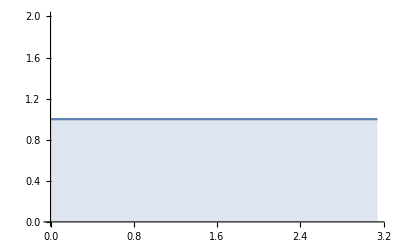

```mathematica
Plot[PowerSpectralDensity[FARIMAProcess[{.0},.0,{0},1],w],{w,0,π},Filling->Axis]
```

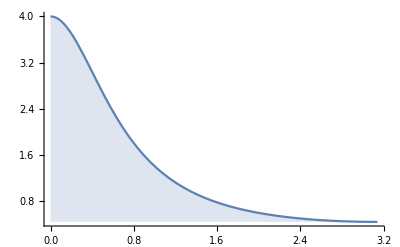

```mathematica
Plot[PowerSpectralDensity[ARProcess[{.5},1],w],{w,0,π},Filling->Axis,PlotRange->All]
```

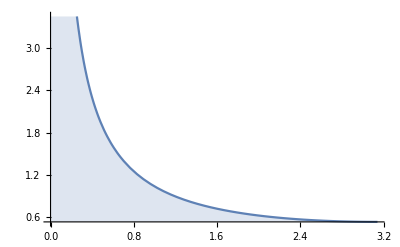

```mathematica
Plot[PowerSpectralDensity[FARIMAProcess[{.0},.45,{0},1],w],{w,0,π},Filling->Axis(*,PlotRange->All*)]
```

## GARCH as an ARMA process

Letting a_t=r_t-μ_t be the mean-corrected log return, the GARCH(𝓂,𝓈) model is defined as:

	a_t=σ_t ϵ_t,
	σ_t^2=α_0+∑_(i=1)^m α_i a_(t-i)^2+∑_(j=1)^s β_j σ_(t-j)^2, 

where {ϵ_t} is i.i.d random variables with zero mean and variance 1,  α_0>0, α_i≥0, β_j≥0, and ∑_(i=1)^(max(m,s)) (α_i+β_i)<1.
The GARCH(𝓂,𝓈) model can be also written with polynomials as:

	σ_t^2=α_0+α(L)a_t^2+β(L)σ_t^2  (*)

where L is the lag operator, α(L)=∑_(i=1)^m α_i L^i and β(L)=∑_(j=1)^s β_j L^j.

Defining ⋁_t =a_t^2-σ_t^2 we can rewrite (*) as an ARMA (p,m) process:

	[1-α(L)-β(L)]a_t^2=α_0+[1-β(L)]⋁_t
	
where p=max{m,s}.

If we allow for the presence of a unit root in [1-α(L)-β(L)], we can define the IGARCH(m,s) model as:

	(1-L)ϕ(L)a_t^2=α_0+[1-β(L)]⋁_t.
	
where ϕ(L)=∑_(i=1)^(s-1) ϕ_i L^i is of order s-1.

## FIGARCH Model

Baillie (1996, JoE) and Bollerslev and Mikkelsen (1996) introduced the FIGARCH process, generalizing the GARCH to allow for persistence in the conditional variance.

If we compare the IGARCH variance equation with the ARFIMA model (1−L)^d ϕ(L)X_t=θ(L)ε_t, we see that we can simply add the long memory term to the GARCH model and define the FIGARCH(m,d,s) model as:

	ϕ(L)(1-L)^d a_t^2=α_0+[1-β(L)]⋁_t.
	
where ϕ(L)=∑_(i=1)^(s-1) ϕ_i L^i is of order s-1.

## FIEGARCH Model

Fractionally Integrated EGARCH (FIEGARCH) model was proposed by Bollerslev and Mikkelsen (1996). The model captures simultaneously with the leverage effect and long-memory.

Let us defines the FIEGARCH(m,d,s) model as
	
	a_t=σ_t ϵ_t
	
	ln(σ_t^2)=α_0+(1+α_1 L+...+α_s L^s)/(1-β_1 L...-β_m L^m)(1-L)^-d g(ϵ_(t-1))
	
	where g(ϵ_t) is defined as:
	
	g(ϵ_t)=θ ϵ_t+γ[|ϵ_t|-E|ϵ_t|].
	
The term (1-L)^-d is the long memory component with the long memory parameter d∈(0,1/2).
When d = 0, the short-memory EGARCH model of Nelson (1991) is obtained.

In its simplest form, the FIEGARCH(1,d,0) model is given by

	(1-β_1 L)(1-L)^d ln(σ_t^2)=α_0+g(ϵ_(t-1))